```mathematica
sourceFolder = "source";
sourcePath = FileNameJoin[{NotebookDirectory[], sourceFolder}];
$Path=Once[Append[$Path,sourcePath]];
<<"SeriesGenerator.wl"
```

# Painleve 1

## Expansion at x=∞

### Getting the Coefficients

The Painleve 1 equation has the form

y''[x] == 6 y[x]^2 - x;

We transform it by defining t = (24 x)^(5/4)/30, y[x] = - √(x/6)( 1 + h[t])

h''[t] + 1/t h'[t] + h[t] ( 1 + 1/2 h[t] ) - 4/(25 t^2)( 1 + h[t] ) == 0

Plug in h[t] ~ ∑_(n=1)^∞ a_n/t^(2n), t→∞   and solve for a_n to some order N

```mathematica
orderN = 50;
coeffs = Painleve1PertSol[orderN];
```

```mathematica
coeffs;
```

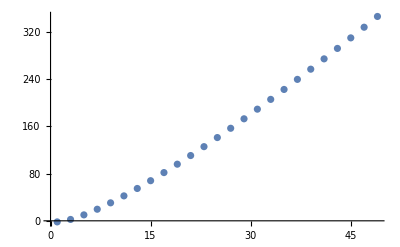

```mathematica
ListPlot[Log@coeffs]
```

### Determining the Growth of the Coefficients

From the Log plot of a_n we see that they grow faster than exponential.
Guessing the growth as

a_n~ c (-1)^(n+1) Γ[2n - 1/2] + ...,    n→∞

We construct new coefficients A_n = a_n/((-1)^(n+1) Γ[2n - 1/2])	and try to find its limit.

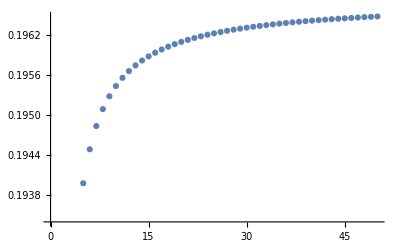

```mathematica
Atable = Table[ coeffs[[i]] / (-1)^(i+1) / Gamma[2i-1/2], {i,1,Length@coeffs}] // N;
ListPlot[Atable]
```

From a Richardson extrapolation we can get a pretty good value for c:

```mathematica
anprefactor = RichardsonExtrapolate[Atable, 6]
Print["The analytic result is ", 1/Pi Sqrt[ 6 / (5 Pi) ] // N]
```

0.196728

The analytic result is 0.196728

#### Higher corrections

a_n~ c (-1)^(n+1) Γ[2n - 1/2] ( 1 - c_2/(2 n - 3/2) + c_3/((2n - 3/2)(2n - 5/2)) - ...)

```mathematica
A2Table = Table[ (Atable[[n]] - anprefactor )(2n - 3/2) , {n,1,Length@Atable}];
```

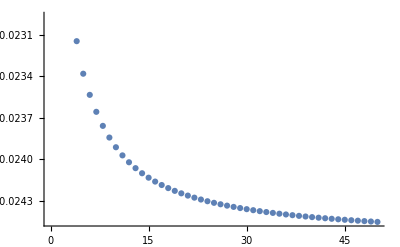

```mathematica
ListPlot[A2Table]
```

```mathematica
c2 = RichardsonExtrapolate[A2Table, 6] / anprefactor
```

-0.125005

```mathematica
1/8 // N
```

0.125

### Borel-Pade Transformation

```mathematica
BT = BorelTransform[coeffs, p];
```

```mathematica
BT;
```

```mathematica
BTcoeffs = BorelTransformCoeffs[coeffs];
```

Use Pade approximant for analytic continuation

```mathematica
PBT = PadeApproximant[BT, {p, 0, {orderN-1, orderN}}]
```

((4 p)/25+(7354314938802028922564280956187890424110644 p^3)/23559694287689146307292406857960790201194375+(5932517523409280633588015177571960073166835743 p^5)/30038610216803661541797818743900007506522828125+(499299767177515592344624094118114245575873232516 p^7)/11264478831301373078174182028962502814946060546875+(1090829177368747266920013622480702936384743986722 p^9)/439314674420753550048793099129537609782896361328125)/(1+(2454272078752116920804978471601681256618874 p^2)/942387771507565852291696274318431608047775+(3866041082026922225947152618708516908602924957 p^4)/1602059211562861948895883666341333733681217500+(1695427040222022625941427186969909853034652371593 p^6)/1802316613008219692507869124634000450391369687500+(8958203993454188610585345614148702676638835547149 p^8)/65083655469741266673895273945116682930799460937500+(2342485726607355110660107376089029347075997013247807 p^10)/536940157625365450059636010047212634179095552734375000)

```mathematica
PBT = Apart[(Numerator@PBT) / FactorCompletely[Denominator@PBT, p], p];
```

```mathematica
poles = p/.NSolve[Denominator@PBT == 0, p];
zeroes = p/.NSolve[Numerator@PBT == 0, p];
BTi = BT/.{p->I p};
PBTi = PBT/.{p->I p};

rePlot = ReImPlot[{BT, PBT} , {p,0,2},
	AxesLabel -> {"Re[p]", "Pade-Borel"},
	PlotLabels -> "Expressions"]
imPlot = ReImPlot[{BTi, PBTi} , {p,0,2},
	AxesLabel -> {"Im[p]", "Pade-Borel"},
	PlotLabels->"Expressions"]
```

-Graphics-

-Graphics-

#### Poles

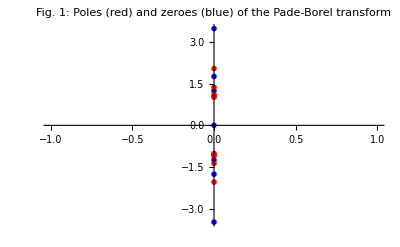

```mathematica
poles = p/.NSolve[Denominator@Together@PBT == 0, p];
zeroes = p/.NSolve[Numerator@PBT == 0, p];

polesPlot = ListPlot[Map[{Re[#], Im[#]}&, poles], PlotStyle->Red,
	PlotMarkers->{Automatic, 0.04}];
zeroesPlot = ListPlot[Map[{Re[#], Im[#]}&, zeroes], PlotStyle->Blue, PlotMarkers->{Automatic, 0.02}];
polesPlotPade = Show[zeroesPlot, polesPlot, PlotLabel->"Fig. 1:\n Poles (red) and zeroes (blue) of the Pade-Borel transform"]
```

### Laplace Transform (Inverse Borel)

```mathematica
<<"SeriesGenerator.wl"
```

```mathematica
xList = Range[0,3.5,0.01];
hList = ParallelMap[InverseBorelTransform[PBT, p, (24 #)^(5/4) / 30]&, xList];
yList = - Sqrt[xList / 6] ( 1 + hList ); (* eq. (4) *)
```

NIntegrate::precw: The precision of the argument function (1. ((5500 (70290347907320568007806895860726017565263417812500+137134991374474083065440826454916069252088164837500 Root[Plus[«6»]&,1,0]+«1»+«1»+1090829177368747266920013622480702936384743986722 Root[«1»&,1,0]^4))/(21082371539466195995940966384801264123683973119230263 (p-√Root[«3»]) (√Root[«1»&,1,0]-√Root[«3»]) «4» (√Root[«1»&,1,0]+√Root[«1»&,4,0]) (√Root[«1»&,1,0]-√Root[«3»]) (√Root[«1»&,1,0]+√Root[«1»&,5,0]))+«17»)) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {2.1111988740733698874283832597394964396497770370917×10^223}. NIntegrate obtained 990444.75523977897282854136614070894939855828002774 and 831627.52948333814227273759889507800567642386296401 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅇ^(-0.00559942 p) ((5500 (70290347907320568007806895860726017565263417812500+137134991374474083065440826454916069252088164837500 Root[«1»]+«1»+«1»+1090829177368747266920013622480702936384743986722 Root[«1»&,1,0]^4))/(21082371539466195995940966384801264123683973119230263 (p-√Root[«3»]) (√Root[«1»&,1,0]-√Root[«3»]) «4» (√Root[«1»&,1,0]+√Root[«1»&,4,0]) (√Root[«1»&,1,0]-√Root[«3»]) (√Root[«1»&,1,0]+√Root[«1»&,5,0]))+«17»)) is less than WorkingPrecision (50.).

NIntegrate::precw: The precision of the argument function (ⅇ^(-0.0133177 p) ((5500 (70290347907320568007806895860726017565263417812500+137134991374474083065440826454916069252088164837500 Root[«1»]+«1»+«1»+1090829177368747266920013622480702936384743986722 Root[«1»&,1,0]^4))/(21082371539466195995940966384801264123683973119230263 (p-√Root[«3»]) (√Root[«1»&,1,0]-√Root[«3»]) «4» (√Root[«1»&,1,0]+√Root[«1»&,4,0]) (√Root[«1»&,1,0]-√Root[«3»]) (√Root[«1»&,1,0]+√Root[«1»&,5,0]))+«17»)) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {320.65169867429683198958901701304291646534385569983}. NIntegrate obtained 0.62345750344398522777211942194304852573564856683771 and 6.568185301102868548383699644273734714655009715631×10^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {320.65169867429683198958901701304291646534385569983}. NIntegrate obtained 0.57744422321280658383380303034653866358027786338105 and 6.3947003441028542262101478877021769419229676778261×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
yPlot = ListPlot[Thread@{xList, yList},
	AxesLabel->{"x", "y(x)"},
	PlotLabel->"Fig. 2",
	PlotLabels -> "ℒ[𝒫ℬ]",
	Joined->True];

tritronquee[x_] := - 0.1875543083 - 0.3049055603 x + 0.1055298557 x^2 - 0.05229396374 x^3;
tritronqueePlot = Plot[tritronquee[x], {x,0,1.8}, PlotStyle->{Gray, Dashed},
	PlotLabels -> "Tritronquee"];
```

```mathematica
Show[yPlot, tritronqueePlot]
```

-Graphics-

### Pole type at p=±i

Using Darboux’s theorem one can find from the large-order growth that it’s a square root branch point.
Following https://epubs.siam.org/doi/10.1137/0139022 :

A function
p(t) = (r(t))/(1 - t/t_1)^-ν + a(t)
r(t) = ∑_(k=0)^∞ b_k(t-t_1)^k analytic in some circle

then p_n ~ (b_0 n^(ν-1))/(t_1^n Gamma[ν])
For some reason I need 2 b_0, I think it’s because there is a conjugate pair of singularities.

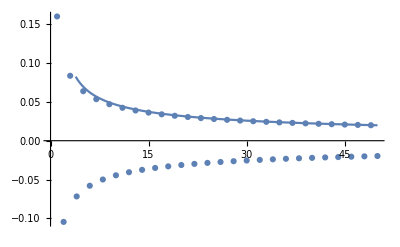

```mathematica
p1 = ListPlot[BTcoeffs];
p2 = Plot[2 * 1/(2 Pi)√(3/5) (n-1)^(1/2-1)/Gamma[1/2], {n,0,50}];
Show[p1,p2]
```

ℬ[h](p) = c/(√(p∓i)),   p→∞

and thus just multiplying ℬ[h](±i) with the square root.

```mathematica
dottedLine = Plot[1 / (2 Pi) Sqrt[3/5], {pp, 0.9, 1}, PlotStyle->{Dashed, Gray},
	PlotLabels->"analytic result"];
singPlotBT = Plot[Re[(Sqrt[p - I] BT) /. p -> I pp], {pp, 0.9, 1.0}, PlotLabels->"Borel"];
singPlotPBT = Plot[Re[(Sqrt[p - I] PBT) /. p -> I pp], {pp, 0.9, 1.0}, PlotStyle->Red,
	PlotLabels->"Pade-Borel"];
Show[dottedLine, singPlotBT, singPlotPBT]
```

-Graphics-

This is not really good, but we can do better

### Conformal Transformation

It turns out to be better to first make a conformal transformation

z = p/(1 + √(1 + p^2))        ⇔    p = (2z)/(1 - z^2)

of the Borel transform, then to expand in a series, make the (analytic continuation) and transform back.

```mathematica
(* Conformal Borel *)
CBT = ConformalMap[BT, p, z];
TCBT = Normal@Series[CBT, {z, 0,2 orderN - 1}]; (* taylor conformal borel *)
PCBT = PadeApproximant[TCBT, {z, 0, {orderN-1, orderN}}];
PCBT = Apart[(Numerator@PCBT) / FactorCompletely[Denominator@PCBT, z], z];
CPCBT = InverseConformalMap[PCBT, z, p];
```

```mathematica
singPlotPCBT = Plot[Re[(Sqrt[p - I] CPCBT) /. p -> I pp], {pp, 0.9, 1.0}, PlotStyle->Black,
	PlotLabels->"Pade-Conformal-Borel"];
Show[dottedLine, singPlotPBT, singPlotBT, singPlotPCBT, PlotRange->All]
```

-Graphics-

```mathematica
Print["We get for half the Stokes constant at p=i: ", Re[(Sqrt[p - I] CPCBT) /. p -> 0.99999 I // N]];
Print["The correct value is: ", 1 / (2 Pi) Sqrt[3/5] // N];
```

We get for half the Stokes constant at p=i: 0.123295

The correct value is: 0.123281

### Why is conformal so much better?

```mathematica
polesPlotPade
```

-Graphics-

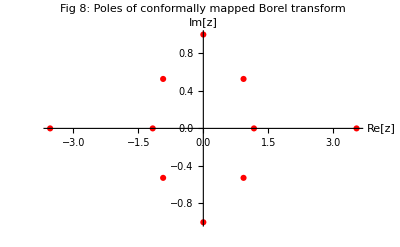

```mathematica
polesC = z/.NSolve[Denominator@Together@PCBT == 0, z];
polesPlotC = ListPlot[Map[{Re[#], Im[#]}&, polesC], PlotStyle->Red,
	AxesLabel->{"Re[z]", "Im[z]"},
	PlotMarkers->{Automatic, 0,04},
	PlotLabel->"Fig 8:\n Poles of conformally mapped Borel transform"]
```

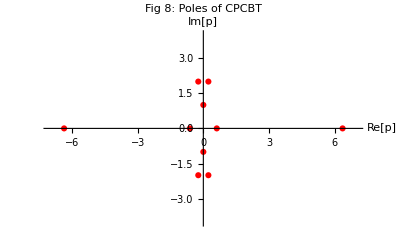

```mathematica
(* z plane poles (conformal) mapped back to Borel plane p *)
polesCPCBT = (2 # / (1 - #^2)&) @ polesC;
polesPlotCPCBT = ListPlot[Map[{Re[#], Im[#]}&, polesCPCBT], PlotStyle->Red,
	AxesLabel->{"Re[p]", "Im[p]"},
	PlotLabel->"Fig 8:\n Poles of CPCBT",
	PlotMarkers->{Automatic, 0,04},
	PlotRange->{{-7,7}, {-4,4}}]
```

### Inverse Borel of Conformal

```mathematica
hListC = ParallelMap[InverseBorelTransform[CPCBT, p, (24 #)^(5/4) / 30]&, xList];
yListC = - Sqrt[xList / 6] ( 1 + hListC ); (* eq. (4) *)
```

NIntegrate::precw: The precision of the argument function (1. ((5500 («6»+133463018347965352048015310026871628207509508973 Root[«1»&,1,0]^4))/(606418606622056857641440026272745147494185702205637 (p/Plus[«2»]-√Root[«3»]) (√Root[«1»&,1,0]-√Root[«3»]) «4» (√Root[«1»&,1,0]+√Root[«1»&,4,0]) (√Root[«1»&,1,0]-√Root[«3»]) (√Root[«1»&,1,0]+√Root[«1»&,5,0]))+«17»)) is less than WorkingPrecision (100.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.500174450396194096517013647759571684561355596817425167863469229211142643187378845787499506060555771×10^223}. NIntegrate obtained 1.274395397374257137118218636407251065270743982550015861574716216078706921144910473903073177538522869×10^1040233 and 1.274395397374257137118218636407251065270743982550015861574716216078706921144910473903073177538522869×10^1040233 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅇ^(-0.00559942 p) ((5500 («6»+133463018347965352048015310026871628207509508973 Root[«1»&,1,0]^4))/(606418606622056857641440026272745147494185702205637 (p/Plus[«2»]-√Root[«3»]) (√Root[«1»&,1,0]-√Root[«3»]) «5» (√Root[«1»&,1,0]-√Root[«3»]) (√Root[«1»&,1,0]+√Root[«1»&,5,0]))+«17»)) is less than WorkingPrecision (100.).

NIntegrate::precw: The precision of the argument function (ⅇ^(-0.0133177 p) ((5500 («6»+133463018347965352048015310026871628207509508973 Root[«1»&,1,0]^4))/(606418606622056857641440026272745147494185702205637 (p/Plus[«2»]-√Root[«3»]) (√Root[«1»&,1,0]-√Root[«3»]) «5» (√Root[«1»&,1,0]-√Root[«3»]) (√Root[«1»&,1,0]+√Root[«1»&,5,0]))+«17»)) is less than WorkingPrecision (100.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {320.5060262069115953712824534785050292489356569439724470852339220795961982813931640680091122835639425}. NIntegrate obtained 1.518292255104131859142718793218644959494352663065363991577466575471514574289698961443220448708055766 and 7.501009136918777491327747932413453354110411281294393632749777714038528771260985359874186399752641301×10^-24 for the integral and error estimates.

```mathematica
yPlotC = ListPlot[Thread@{xList, yListC},
	AxesLabel->{"x", "y(x)"},
	Joined->True,
	PlotStyle->Red,
	PlotRange->{{0,0.3},{-0.8,0}},
	PlotLabels->"Pade-Comformal-Borel"];
```

```mathematica
Show[yPlot, tritronqueePlot]
```

-Graphics-

```mathematica
Show[yPlot, tritronqueePlot, yPlotC, PlotRange->{{0,0.3}, {-0.17,-0.27}}, Frame->True]
```

-Graphics-

## Reexpansion Closer to Origin